```mathematica
ClearAll["Global`*"];
storage="/Volumes/home/BEM/";
(*case="moon_pool_no_a0d8_";*)
case="moon_pool_no_a0d8_";
data[5.0]=Import[storage<>case<>"T5d0_h80/result.json"];
data[5.5]=Import[storage<>case<>"T5d5_h80/result.json"];
data[6.0]=Import[storage<>case<>"T6d0_h80/result.json"];
data[6.5]=Import[storage<>case<>"T6d5_h80/result.json"];
data[7.0]=Import[storage<>case<>"T7d0_h80/result.json"];
data[7.5]=Import[storage<>case<>"T7d5_h80/result.json"];
data[8.0]=Import[storage<>case<>"T8d0_h80/result.json"];
data[8.5]=Import[storage<>case<>"T8d5_h80/result.json"];
data[9.0]=Import[storage<>case<>"T9d0_h80/result.json"];
data[9.5]=Import[storage<>case<>"T9d5_h80/result.json"];
data[10.0]=Import[storage<>case<>"T10d0_h80/result.json"];
```

```mathematica
(*(*Recreate*)
dt=0.01;
min=10;
max=90;
Do[
DATA=data[T];
Time[T]=Table[t,{t,min,max,dt}];
Module[{tmp},
tmp=Interpolation[Transpose[{"time"/.DATA,("floatingbody_pitch"/.DATA)}]];
intpPitch[T]=Table[tmp[t],{t,min,max,dt}];
];
Module[{tmp},
tmp=Interpolation[Transpose[{"time"/.DATA,(("floatingbody_COM"/.DATA)ᵀ[[3]]-75)}]];
intpHeave[T]=Table[tmp[t],{t,min,max,dt}];
];
Module[{tmp},
tmp=Interpolation[Transpose[{"time"/.DATA,(("floatingbody_COM"/.DATA)ᵀ[[1]]-200)}]];
intpSurge[T]=Table[tmp[t],{t,min,max,dt}];
]
,{T,5.0,10.0,.5}]
fftPitch[T_]:=With[{n=Length[Time[T]]},Return[2*Abs@Fourier[intpPitch[T][[;;-1]],FourierParameters->{-1, 1}]];];
fftHeave[T_]:=With[{n=Length[Time[T]]},Return[2*Abs@Fourier[intpHeave[T][[;;-1]],FourierParameters->{-1, 1}]];];
fftSurge[T_]:=With[{n=Length[Time[T]]},Return[2*Abs@Fourier[intpSurge[T][[;;-1]],FourierParameters->{-1, 1}]];];
getPeriod[T_]:=Module[{t,n},t=Time[T];n=Length[t];Return@Table[(i/(n*(If[i+1>n,t[[i]]-t[[i-1]],t[[i+1]]-t[[i]]])))^-1,{i,1,n,1}]];
getTime[T_]:=Module[{},Return[(Time[T])];];
ListPlot[Table[Transpose[{Table[i/(max-min),{i,Length[fftPitch[T]]}],fftPitch[T]}][[;;20]],{T,5.5,10.,0.5}],PlotRange->All,Joined->True]*)
```

```mathematica
fftPitch[T_]:=With[{n=Length["time"/.data[T]]},Return[2*Abs@Fourier[("floatingbody_pitch"/.data[T])[[;;-1]],FourierParameters->{-1, 1}]];];
fftHeave[T_]:=With[{n=Length["time"/.data[T]]},Return[2*Abs@Fourier[(("floatingbody_COM"/.data[T])ᵀ[[3]]-75)[[;;-1]],FourierParameters->{-1, 1}]];];
fftSurge[T_]:=With[{n=Length["time"/.data[T]]},Return[2*Abs@Fourier[(("floatingbody_COM"/.data[T])ᵀ[[1]]-200)[[;;-1]],FourierParameters->{-1, 1}]];];
(*getPeriod[data_]:=With[{timelist="time"/.data,n=Length[timelist],dt=0.2},Return@Table[(i/(n*dt))^-1,{i,1,n,1}]];*)
getPeriod[T_]:=Module[{t,n},t="time"/.data[T];n=Length[t];Return@Table[(i/(n*(If[i+1>n,t[[i]]-t[[i-1]],t[[i+1]]-t[[i]]])))^-1,{i,1,n,1}]];
getTime[T_]:=Module[{},Return[("time"/.data[T])];];
```

```mathematica
(*Do[data75[[i]][[2]]=data75[[i]][[2]][[;;547]],{i,1,Length[data75]}]*)
```

```mathematica
Length@data[5.0]
Length@fftPitch[data[5.0]]
Length@getPeriod[data[5.0]]
Column@data[5.0][[;;,1]]
```

16

ReplaceAll::reps: {data[{floatingbody_accel→{{0.0000341521,0.0000115008,-0.0301331,2.99754×10^-6,3.98594×10^-7,1.89093×10^-7},{0.0000621054,0.0000528618,-0.0289623,1.83637×10^-6,2.11127×10^-6,9.36395×10^-7},{0.0000838325,0.0000881335,-0.0271496,8.32536×10^-7,4.2893×10^-6,1.62723×10^-6},{0.000106188,0.000108905,-0.0247268,-1.97253×10^-8,6.67432×10^-6,2.11471×10^-6},«4»,{0.0001971,0.0000179605,-0.00690317,-1.87136×10^-6,8.77004×10^-6,1.53054×10^-7},{0.000211239,-7.37689×10^-6,-0.00278151,-1.87547×10^-6,7.59016×10^-6,-6.9776×10^-7},«290»},«9»,«6»}]}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Fourier::fftl: 引数floatingbody_pitch/.data[{floatingbody_accel→{{0.0000341521,0.0000115008,-0.0301331,2.99754×10^-6,3.98594×10^-7,1.89093×10^-7},{0.0000621054,0.0000528618,-0.0289623,1.83637×10^-6,2.11127×10^-6,9.36395×10^-7},{0.0000838325,0.0000881335,-0.0271496,8.32536×10^-7,4.2893×10^-6,1.62723×10^-6},«5»,{0.0001971,0.0000179605,-0.00690317,-1.87136×10^-6,8.77004×10^-6,1.53054×10^-7},{0.000211239,-7.37689×10^-6,-0.00278151,-1.87547×10^-6,7.59016×10^-6,-6.9776×10^-7},«290»},floatingbody_velocity→{«1»},«7»,floatingbody_roll→{6.311×10^-8,2.28594×10^-7,«8»,«290»},«6»}]は数量の非空のリストでも矩形配列でもありません．

2

ReplaceAll::reps: {data[{floatingbody_accel→{{0.0000341521,0.0000115008,-0.0301331,2.99754×10^-6,3.98594×10^-7,1.89093×10^-7},{0.0000621054,0.0000528618,-0.0289623,1.83637×10^-6,2.11127×10^-6,9.36395×10^-7},{0.0000838325,0.0000881335,-0.0271496,8.32536×10^-7,4.2893×10^-6,1.62723×10^-6},{0.000106188,0.000108905,-0.0247268,-1.97253×10^-8,6.67432×10^-6,2.11471×10^-6},«4»,{0.0001971,0.0000179605,-0.00690317,-1.87136×10^-6,8.77004×10^-6,1.53054×10^-7},{0.000211239,-7.37689×10^-6,-0.00278151,-1.87547×10^-6,7.59016×10^-6,-6.9776×10^-7},«290»},«9»,«6»}]}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

2

floatingbody_accel
floatingbody_velocity
floatingbody_COM
floatingbody_force
floatingbody_torque
floatingbody_EK
floatingbody_EP
floatingbody_area
floatingbody_pitch
floatingbody_roll
floatingbody_yaw
time
water_E
water_EK
water_EP
water_volume

## Pitch

```mathematica
(*Peridos to check*)
Ts={6.5,7.0,7.5,8.0,8.5,9.0,9.5,10.};
```

```mathematica
commonOptions2D=Sequence[
AspectRatio->1/2,
Joined->True,
Frame->True,
PlotStyle->Table[{ColorData[90,"ColorList"][[i]],{Dashed,Normal}[[Mod[i,2]+1]]},{i,1,10}],
ImageSize->Large,
AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
FrameStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
LabelStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}],
PlotLegends->LineLegend[Table[T,{T,Ts}],LegendLabel->"Incident wave\n period T[s]",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],
FrameStyle->Black];
commonOptions3D=Sequence[TicksStyle->Black,ImageSize->Medium,AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}]];
```

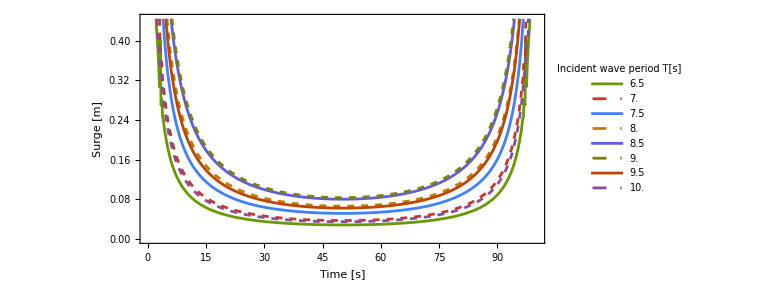

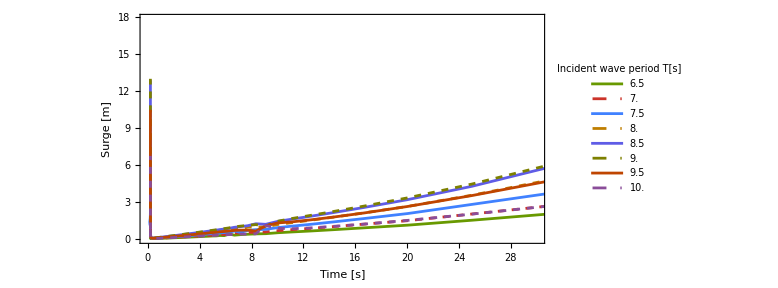

```mathematica
ListPlot[Table[Transpose[{getTime[T],fftSurge[T]}],{T,Ts}]
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Surge [m]"}
,PlotLegends->Table[T,{T,Ts}]
]

ListPlot[Table[Transpose[{getPeriod[T],fftSurge[T]}],{T,Ts}]
,PlotRange->{{0,30},All}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Surge [m]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
]

(*ListPlot3D[Transpose[Table[{getPeriod[T],fftHeave[T],fftSurge[T]},{T,Ts}]],
PlotRange->{{0.1,14},{5,10},{0,4*10^-3}}
,Evaluate@commonOptions3D
,AxesLabel->{"Period [s]","Incident [m]","FFT"}
,ColorFunction->"SouthwestColors"
]*)
```

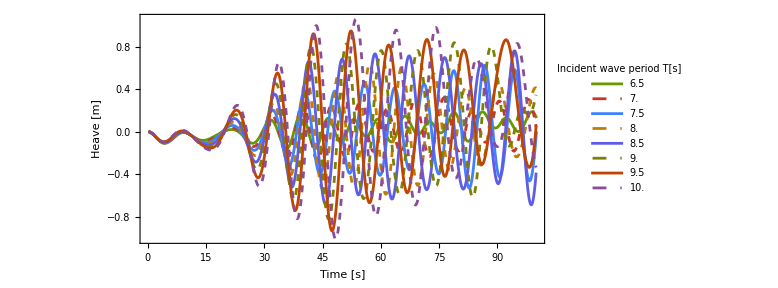

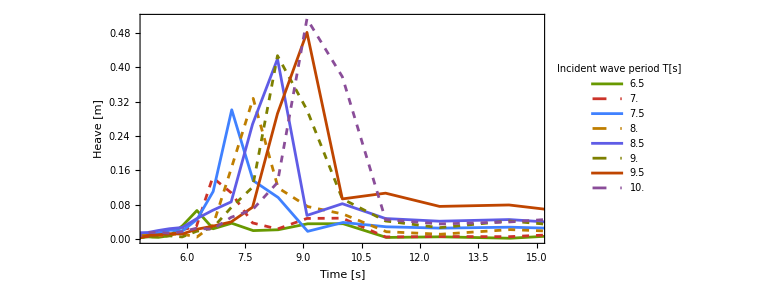

-Graphics3D-

```mathematica
ListPlot[Table[Transpose[{"time"/.d,("floatingbody_COM"/.d)ᵀ[[3]]-75}],{d,Table[data[T],{T,Ts}]}]
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Heave [m]"}
,PlotLegends->Table[T,{T,Ts}]
]

ListPlot[Table[Transpose[{getPeriod[d],fftHeave[d]}],{d,Table[data[T],{T,Ts}]}]
,PlotRange->{{5,15},All}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Heave [m]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
]

ListPlot3D[Flatten[Table[Transpose[{getPeriod[d[[2]]],Table[d[[1]],{i,1,Length[getPeriod[d[[2]]]]}],fftHeave[d[[2]]]}],{d,Table[{T,data[T]},{T,Ts}]}],1],
PlotRange->{{2,14},{5,10},{0,10^-1}}
,Evaluate@commonOptions3D
,AxesLabel->{"Period [s]","Incident [m]","FFT"}
,ColorFunction->"SouthwestColors"
]
```

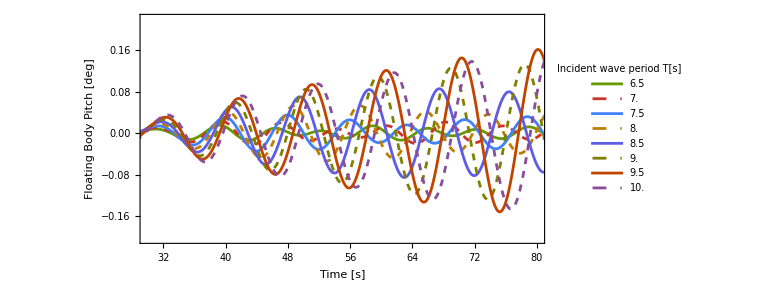

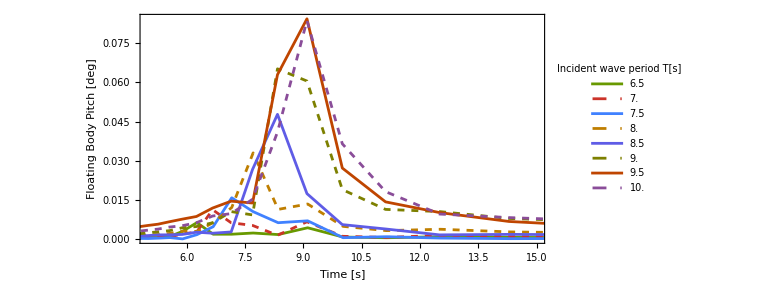

-Graphics3D-

```mathematica
ListPlot[Table[Transpose[{"time"/.d,"floatingbody_pitch"/.d}],{d,Table[data[T],{T,Ts}]}]
,PlotRange->{{30,80},All}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Floating Body Pitch [deg]"}
,PlotLegends->Table[T,{T,Ts}]
]

ListPlot[Table[Transpose[{getPeriod[d],fftPitch[d]}],{d,Table[data[T],{T,Ts}]}]
,PlotRange->{{5,15},All}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Floating Body Pitch [deg]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
]

ListPlot3D[Flatten[Table[Transpose[{getPeriod[d[[2]]],Table[d[[1]],{i,1,Length[getPeriod[d[[2]]]]}],fftPitch[d[[2]]]}],{d,Table[{T,data[T]},{T,Ts}]}],1],
PlotRange->{{2,14},{5,10},{0,4*10^-3}}
,Evaluate@commonOptions3D
,AxesLabel->{"Period [s]","Incident [m]","FFT"}
,ColorFunction->"SouthwestColors"
]
```